Project 10 : Linearization
Jacob Schnoor

System 1

f1 = x y
f2 = -x^2-y
Equilibria:

@(0,0)		Jacobian Matrix = (0 | 0
0 | -1)
			Eigenpairs : {-1. , (0.
1.)}	{0. ,(1.
0.)}

Predictions:
	The first eigenvector at (0,0) is (0,1) meaning the influence on the arrows will be directly vertical. The corresponding eigenvalue is negative meaning arrows will pulled into the point (0,0) from both above and below. The second eigenvector is (1,0) meaning the influence will be perfectly horizontal. The corresponding eigenvalue is zero meaning that arrows will be neither pushed nor pulled by the point. Instead at the line y=0, all arrows will point fully up or down.

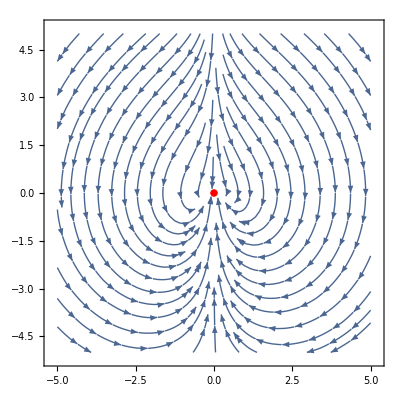

System 2

f1 = -x^2+y^2
f2 = 2 x
Equilibria:

@(0,0)		Jacobian Matrix = (0 | 0
2 | 0)
			Eigenpairs : {0. , (0.
1.)}	{0. ,(0.
0.)}

Predictions:
	The first eigenvector for (0,0) is (0,1). The influence on streamplot arrows will again be vertical. The corresponding eigenvalue is zero however meaning arrows are neither pushed nor pulled toward the point (0,0). At the line x=0, the arrows will point fully left or right. The second eigenvector is (0,0) meaning it has no direction of influence over the arrows. The arrows simply act as if there is only the first eigenvector.

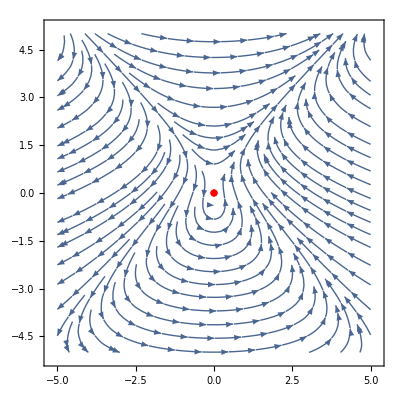

System 3

f1 = Log[x+y]
f2 = x y
Equilibria:

@(0,1)		Jacobian Matrix = (1 | 1
1 | 0)
			Eigenpairs : {1.61803 , (1.61803
1.)}	{-0.618034 ,(-0.618034
1.)}

@(1,0)		Jacobian Matrix = (1 | 1
0 | 1)
			Eigenpairs : {1. , (1.
0.)}	{1. ,(0.
0.)}

Predictions:
	To start off, x’ will not even have a defined value all throughout the graph. It is equal to Log[x+y] meaning when x+y<=0, the function will have no solution. About half of the graph will be white space. Aside from that, there are two separate equilibria in this system: (0,1) and (1,0)

For (0,1) the first eigenvector is about (1.6,1) meaning the direction of influence will be up and to the right. The corresponding eigenvalue is positive meaning the arrows will be repelled away. The second eigenvector is about (-0.6,1) which influences arrows that are up and to the left. These arrows will be pulled closer to the point because the eigenvalue is negative.

For (1,0) the first eigenvector is (1,0) meaning influence will be horizontal and the positive eigenvalue suggests that arrows will be pushed outwards from the point, either to the left or right. The second eigenvector is (0,0) and therefore directionless and non-influential

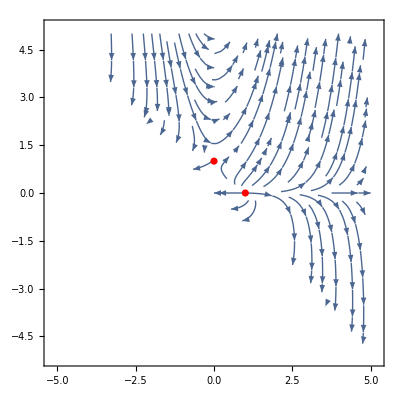

System 4

f1 = x^3+y
f2 = -x-y^3
Equilibria:

@(-1,1)		Jacobian Matrix = (3 | 1
-1 | -3)
			Eigenpairs : {-2.82843 , (-0.171573
1.)}	{2.82843 ,(-5.82843
1.)}

@(0,0)		Jacobian Matrix = (0 | 1
-1 | 0)
			Eigenpairs : {0.+1. ⅈ , (0.-1. ⅈ
1.)}	{0.-1. ⅈ ,(0.+1. ⅈ
1.)}

@(1,-1)		Jacobian Matrix = (3 | 1
-1 | -3)
			Eigenpairs : {-2.82843 , (-0.171573
1.)}	{2.82843 ,(-5.82843
1.)}

Predictions:
	This system has three separate points of equilibrium: (-1,1),(0,0),(1,-1)

For the point (0,0), both eigenvectors consist of imaginary components. They are (-i,1) and (i,1) respectively. In situations like this, either an ellipse or spiral is formed based on the value of p in the expression p+qi. For this instance, p is equal to zero suggesting that it will only be ellipses that form close to the point (0,0).

The points (-1,1) and (1,-1) have equivalent eigenpairs meaning the arrow behavior relative to each point will be the same. The first eigenvector is about (-0.2,1) meaning it will influence arrows that are above and slightly to the left or below and slightly to the right. The eigenvalue is negative meaning it will pull these arrows inward to the point. The other eigenvector is about (-5.8, 1) which will influence arrows to the left that are slightly above or arrows to the right that are slightly below. The eigenvalue is positive suggesting it will push these away from the point.

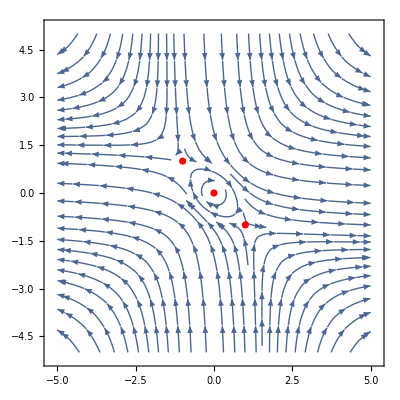

System 1 Modified : ϵ = -4

f1 = x (-4+y)
f2 = -x^2-y
Equilibria:

@(0,0)		Jacobian Matrix = (-4 | 0
0 | -1)
			Eigenpairs : {-4. , (1.
0.)}	{-1. ,(0.
1.)}

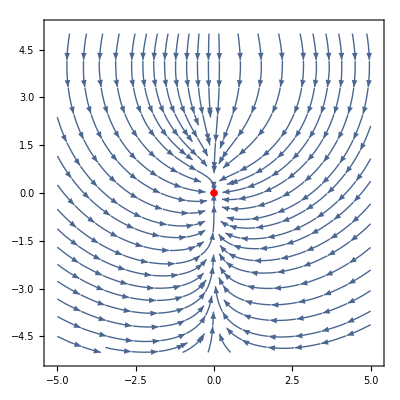

System 1 Modified : ϵ = -2

f1 = x (-2+y)
f2 = -x^2-y
Equilibria:

@(0,0)		Jacobian Matrix = (-2 | 0
0 | -1)
			Eigenpairs : {-2. , (1.
0.)}	{-1. ,(0.
1.)}

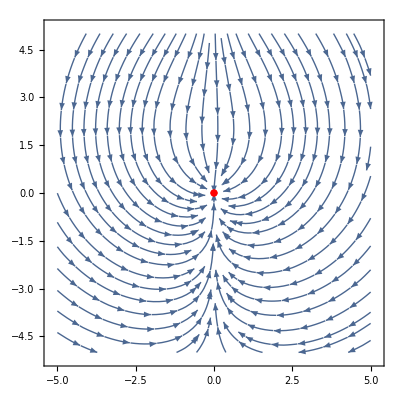

System 1 Modified : ϵ = 0

f1 = x y
f2 = -x^2-y
Equilibria:

@(0,0)		Jacobian Matrix = (0 | 0
0 | -1)
			Eigenpairs : {-1. , (0.
1.)}	{0. ,(1.
0.)}

-Graphics-

System 1 Modified : ϵ = 2

f1 = x (2+y)
f2 = -x^2-y
Equilibria:

@(0,0)		Jacobian Matrix = (2 | 0
0 | -1)
			Eigenpairs : {2. , (1.
0.)}	{-1. ,(0.
1.)}

@(-√2,-2)		Jacobian Matrix = (0 | -√2
2 √2 | -1)
			Eigenpairs : {-0.5+1.93649 ⅈ , (0.176777+0.684653 ⅈ
1.)}	{-0.5-1.93649 ⅈ ,(0.176777-0.684653 ⅈ
1.)}

@(√2,-2)		Jacobian Matrix = (0 | √2
-2 √2 | -1)
			Eigenpairs : {-0.5+1.93649 ⅈ , (-0.176777-0.684653 ⅈ
1.)}	{-0.5-1.93649 ⅈ ,(-0.176777+0.684653 ⅈ
1.)}

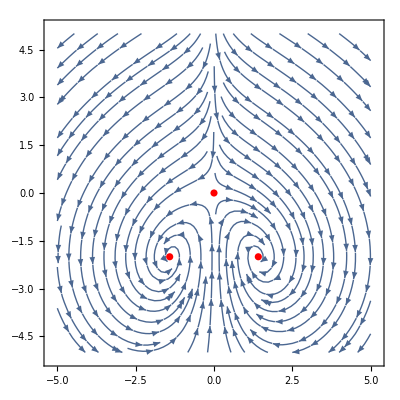

System 1 Modified : ϵ = 4

f1 = x (4+y)
f2 = -x^2-y
Equilibria:

@(-2,-4)		Jacobian Matrix = (0 | -2
4 | -1)
			Eigenpairs : {-0.5+2.78388 ⅈ , (0.125+0.695971 ⅈ
1.)}	{-0.5-2.78388 ⅈ ,(0.125-0.695971 ⅈ
1.)}

@(0,0)		Jacobian Matrix = (4 | 0
0 | -1)
			Eigenpairs : {4. , (1.
0.)}	{-1. ,(0.
1.)}

@(2,-4)		Jacobian Matrix = (0 | 2
-4 | -1)
			Eigenpairs : {-0.5+2.78388 ⅈ , (-0.125-0.695971 ⅈ
1.)}	{-0.5-2.78388 ⅈ ,(-0.125+0.695971 ⅈ
1.)}

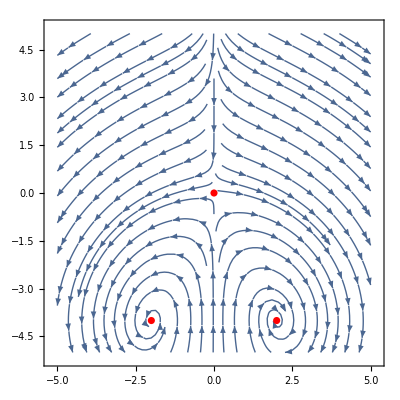

```mathematica
fones={x*y,(y^2)-(x^2),Log[x+y],y+(x^3)};
ftwos={-y-x^2,2*x,x*y,-x-(y^3)};
predicts={"The first eigenvector at (0,0) is (0,1) meaning the influence on the arrows will be directly vertical. The corresponding eigenvalue is negative meaning arrows will pulled into the point (0,0) from both above and below. The second eigenvector is (1,0) meaning the influence will be perfectly horizontal. The corresponding eigenvalue is zero meaning that arrows will be neither pushed nor pulled by the point. Instead at the line y=0, all arrows will point fully up or down.
",
"The first eigenvector for (0,0) is (0,1). The influence on streamplot arrows will again be vertical. The corresponding eigenvalue is zero however meaning arrows are neither pushed nor pulled toward the point (0,0). At the line x=0, the arrows will point fully left or right. The second eigenvector is (0,0) meaning it has no direction of influence over the arrows. The arrows simply act as if there is only the first eigenvector.
",
"To start off, x’ will not even have a defined value all throughout the graph. It is equal to Log[x+y] meaning when x+y<=0, the function will have no solution. About half of the graph will be white space. Aside from that, there are two separate equilibria in this system: (0,1) and (1,0)

For (0,1) the first eigenvector is about (1.6,1) meaning the direction of influence will be up and to the right. The corresponding eigenvalue is positive meaning the arrows will be repelled away. The second eigenvector is about (-0.6,1) which influences arrows that are up and to the left. These arrows will be pulled closer to the point because the eigenvalue is negative.

For (1,0) the first eigenvector is (1,0) meaning influence will be horizontal and the positive eigenvalue suggests that arrows will be pushed outwards from the point, either to the left or right. The second eigenvector is (0,0) and therefore directionless and non-influential
",
"This system has three separate points of equilibrium: (-1,1),(0,0),(1,-1)

For the point (0,0), both eigenvectors consist of imaginary components. They are (-i,1) and (i,1) respectively. In situations like this, either an ellipse or spiral is formed based on the value of p in the expression p+qi. For this instance, p is equal to zero suggesting that it will only be ellipses that form close to the point (0,0).

The points (-1,1) and (1,-1) have equivalent eigenpairs meaning the arrow behavior relative to each point will be the same. The first eigenvector is about (-0.2,1) meaning it will influence arrows that are above and slightly to the left or below and slightly to the right. The eigenvalue is negative meaning it will pull these arrows inward to the point. The other eigenvector is about (-5.8, 1) which will influence arrows to the left that are slightly above or arrows to the right that are slightly below. The eigenvalue is positive suggesting it will push these away from the point.
"};
For[i=1,i≤4,i++,
f1=fones[[i]];
f2=ftwos[[i]];
temp=Solve[f1==0&&f2==0,{x,y},Reals];
Print[Style["\n\nSystem ",Blue,Italic,24],Style[i,Blue,Italic,24]];
Print["f1 = ",f1,"\nf2 = ", f2,"\nEquilibria: "];
dim=Dimensions[temp];
For[j=1,j≤dim[[1]],j++,
x0=temp[[j,1,2]];
y0=temp[[j,2,2]];
J=D[{f1,f2},{{x,y}}];
	A=MatrixForm[J/.{x->x0,y->y0}];
eigens=Eigenvalues[J/.{x->x0,y->y0}];
eigenvs=Eigenvectors[J/.{x->x0,y->y0}];
Print["\n@(",x0,",",y0,")\t\tJacobian Matrix = ",A,"\n\t\t\tEigenpairs : {",eigens[[1]]//N," , ",MatrixForm[eigenvs[[1]]]//N,"}\t{",eigens[[2]]//N," ,",MatrixForm[eigenvs[[2]]]//N,"}"];
];
Print["\nPredictions:\n\t",predicts[[i]],"\n"];
pl1=StreamPlot[{f1,f2},{x,-5,5},{y,-5,5}];
pl2=ListPlot[Table[temp[[m,n,2]],{m,dim[[1]]},{n,2}],PlotStyle->Red];
Print[Show[pl1,pl2]];
];
For[i=1,i≤5,i++,
f1=x(y+2(i-3));
f2=ftwos[[1]];
temp=Solve[f1==0&&f2==0,{x,y},Reals];
Print[Style["\n\nSystem 1 Modified : ϵ = ",Blue,Italic,24],Style[2(i-3),Blue,Italic,24]];
Print["f1 = ",f1,"\nf2 = ", f2,"\nEquilibria: "];
dim=Dimensions[temp];
For[j=1,j≤dim[[1]],j++,
x0=temp[[j,1,2]];
y0=temp[[j,2,2]];
J=D[{f1,f2},{{x,y}}];
	A=MatrixForm[J/.{x->x0,y->y0}];
eigens=Eigenvalues[J/.{x->x0,y->y0}];
eigenvs=Eigenvectors[J/.{x->x0,y->y0}];
Print["\n@(",x0,",",y0,")\t\tJacobian Matrix = ",A,"\n\t\t\tEigenpairs : {",eigens[[1]]//N," , ",MatrixForm[eigenvs[[1]]]//N,"}\t{",eigens[[2]]//N," ,",MatrixForm[eigenvs[[2]]]//N,"}"];
];
pl1=StreamPlot[{f1,f2},{x,-5,5},{y,-5,5}];
pl2=ListPlot[Table[temp[[m,n,2]],{m,dim[[1]]},{n,2}],PlotStyle->Red];
Print[Show[pl1,pl2]];
];
```

Possible Behaviors for System 1:
	When ϵ>0, there exist three equilibria in the solution. Otherwise it is only a single point of equilibrium. Greater values of ϵ cause the three points to drift further and further apart on the graph. The point (0,0) acts most directly on the arrows above and below it, pulling them inward. In some cases, it appears to resemble an upside down heart. The other two points are symmetrical and continue to move down and away from the center as ϵ→∞. They act opposite to one another with the point on the right spiralling clockwise while the one on the left spirals counterclockwise.